### Initialization

```mathematica
SetDirectory["/Users/jsquire/Dropbox/WorkDocuments/Accretion\ Disks"];
Get["NMStools`"]
ParallelNeeds["NMStools`"]

ClearAll@createInPMats
(*Creates inner product matrices for Chebyshev eigenfunctions, see Reddy, Schmid, Henningson, SIAM J. Appl. Math., 53 15 (1993)*)

(*len is Npoly plus number of BCs*)
Options[createInPMats]={precision->MachinePrecision};
createInPMats[len_,mattype_String,zfuncs_:{},OptionsPattern[]]:=
Module[{Lmat,len1,len2,cmat},
{len1,len2}=If[Head[len]===List,len,{len,len}];
Lmat=Table[If[OddQ[k+j],0,1/(1-(j+k)^2)+1/(1-(j-k)^2)],{j,0,len1},{k,0,len2}];
N[
Switch[mattype,
"L2",Lmat,
"H2",(constructDmat[1,{len1+1,len2+1}]†).Lmat.constructDmat[1,{len1+1,len2+1}],
"zero",ConstantArray[0,{len1+1,len2+1}],
"gen",
cmat=generalChebyMat[{len1,len2},zfuncs,precision->OptionValue[precision]];
(cmat†).Lmat.cmat],
OptionValue[precision]]
]
```

### Advection equation example

#### Spectrum from EigenNDSolve

```mathematica
?EigenNDSolve
```

EigenNDsolve[eqns, vars, range, evalvar, Options]
Solves the list of eqns for the eigenfunctions and eigenvalues using a spectral expansion
in Chebyshev polynomials.
vars is a list of the dependent variables, 
range is a list with {indepentent variable, min, max} (as for NDSolve),
evalvar is the eigenvalue parameter (must be linear in this).

Options:
Npoly→80 - Number of polynomials to use in Chebyshev expansion (actually Npoly+1 due to T_0)
returnInterp→True - If True, returns the eigenfunctions as InterpolatingFunction objects.
	If False, returns a list of the Chebyshev coefficients for each eigenstate.
noRowReduce→False - If True, over-rides solving for the boundary conditions and forming a
	reduced matrix.
precision→MachinePrecision - Precision of the calculation. If not MachinePrecision,
	calculation will be much slower; however this is necessary for accurate calculation
	with certain types of problems.
returnMatrix->False - With normal inputs, returns a the Chebyshev matrix. If the output is 
	then used as eqns, it skips calculating the matrix. Useful for parameter scans.

```mathematica
?plotEValues
```

plotEValues[evalues, range, Options]
Plots eigenvalues in a convenient way, displaying their value and number with a mouse-over.
range is a nested list {x_range, y_range}.

Options:
estateList->False - List of eigen-functions to plot when a given point is clicked.

Example of advection diffusion equation, ∂_t f + U_0∂_x f=η(∂_x)^2 f

```mathematica
polynum=120;U0=1;ηdiss = 0.04;
advectionSpec=EigenNDSolve[Join[{-ⅈ ω u[x]+U0 u'[x]==ηdiss u''[x]},
{u[-1]==0,u[1]==0}],{u},{x,-1,1},ω,Npoly->polynum,precision->MachinePrecision,noRowReduce->True,returnInterp->False,parallel->False];
(* Plot spectrum and modes, all centered around right boundary *)
plotEValues[First@advectionSpec,{{-1,1},{-200,0.1}},estateList->Rest@eigsToInterp@advectionSpec]
```

#### Calculation of pseudo-modes

```mathematica
?pseudoModes
```

pseudoModes[esys, K, inP, Options]
Returns functions to calculate the spatial structure and growth of the fastest growing 
pseudo-modes at a given time.
esys is the list of eigenvalues and eigenvectors.
K is the number of eigenvectors to use in calculating fastest growing mode.
inP is the inner product to use. This can be either a matrix, in which case the inner
	product is assumed to be v†.M.v, or a function taking arguments of the form 
	inP[{{ξ_1,ξ_2},{η_1,η_2},...}] where {ξ, η,...} are the dependent variables.
Output functions, {G[t],ξ[t]}
G[t] is the maximum growth at a given time
ξ[t,t_0] is the perturbation at time t that maximizes the growth at t_0

Options:
cholPrecision→MachinePrecision - Precision used in calculating the Cholesky factorizations
	and Hermitian matrices. May need to be increased if PositiveDefinite warning encountered.
HermitianFixϵ→10^-14 - Adds ϵ DiagonalMatrix to matrix before taking CholeskyFactorization, to 
	help make it positive definite. Safer to increase cholPrecision. 
removeLarEvalsCutoff→10^3 - Automatically remove any eigenvalues that are larger than this.

```mathematica
(* Create inner product matrix. Formed in Chebyshev basis for speed *)
inPmat =Module[{pc=precision->30},SparseArray[{Band[{1,1}]->(createInPMats[polynum+2, "L2",{},pc])},
{#,#}&@((polynum+1)+2)]
];
(* Allows simple evaluation of norm of a given solution *)
inPfunc[chebsol_]:=Block[{fullvec={Join@@chebsol}ᵀ},
(fullvec†.inPmat.fullvec)⟦1,1⟧];
(* Calculate G(t) and pseudomodes *)
{Gfun,solfun}=pseudoModes[N[advectionSpec],80,inPmat,cholPrecision->30,HermitianFixϵ->0];
```

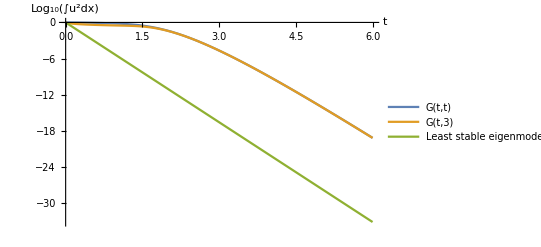

```mathematica
(* Plot the amplitudes of the eigenmode and pseudomode (this is a little slow because of all of the solfun evaluations*)
gplot = Plot[{Log10[Gfun[tp]],Log10[inPfunc[solfun[tp,3]]/Evaluate@inPfunc[solfun[0,3]]],Log10[Exp[2Im@advectionSpec⟦1,1⟧ tp]]},{tp,0,6},PlotRange->All,AxesLabel->{"t","Log_10(∫u^2dx)"},PlotLegends->{"G(t,t)","G(t,3)","Least stable eigenmode"}]
```

```mathematica
(* Plot the solution in time, it starts on the left boundary which allows it to not decay for much longer than the eigenmodes*)
Manipulate[
DynamicModule[{sol},
sol=funcFromCheby[solfun[t,3]⟦1⟧,{-1,1}];
Plot[Abs[sol[x]],{x,-1,1},PlotRange->All]],
{t,0,6}]
```